```mathematica
?Solve
```

RowBox[{"Solve", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["vars", "TI"]}], "]"}] attempts to solve the system StyleBox["expr", "TI"] of equations or inequalities for the variables StyleBox["vars", "TI"]. 
RowBox[{"Solve", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["vars", "TI"], ",", StyleBox["dom", "TI"]}], "]"}] solves over the domain StyleBox["dom", "TI"]. Common choices of StyleBox["dom", "TI"] are Reals, Integers, and Complexes.

```mathematica
Solve[t^2+t+a==0,t]
```

{{t→1/2 (-√(1-4 a)-1)},{t→1/2 (√(1-4 a)-1)}}

```mathematica
D[Sin[x], x]
```

cos(x)

```mathematica
∫t^a ⅆt
```

t^(a+1)/(a+1)

```mathematica
Series[f[t],{t,0,3}]
```

f(0)+t f'(0)+1/2 t^2 f''(0)+1/6 f^(3)(0) t^3+O(t^4)

```mathematica
∑_(n=1)^10 (1/2)^n
```

1023/1024

```mathematica
LaplaceTransform[Sin[t],t, s]
```

1/(s^2+1)

```mathematica
DSolve[D[u[t], t]+α u[t] == 0, u, t]
```

{{u→({t}↦c_1 ⅇ^(α (-t)))}}

```mathematica
DSolve[D[u[t], t]+α u[t] == 0, u, t]
```

{{u→({t}↦c_1 ⅇ^(α (-t)))}}

```mathematica
<<"VectorAnalysis`"
```

```mathematica
CrossProduct[{a,b,c},{d,e,f}]
```

{b f-c e,c d-a f,a e-b d}

```mathematica
CrossProduct[{a,b,c},{d,e,f}]//MatrixForm
```

(b f-c e
c d-a f
a e-b d)

```mathematica
Grad[f[x,y,z],Cartesian[x,y,z]]//MatrixForm
```

(f^(1,0,0)(x,y,z)
f^(0,1,0)(x,y,z)
f^(0,0,1)(x,y,z))

```mathematica
NSolve[x^6+x^2-1==0,x]
```

{{x→-0.826031},{x→-0.659334-0.880844 ⅈ},{x→-0.659334+0.880844 ⅈ},{x→0.659334-0.880844 ⅈ},{x→0.659334+0.880844 ⅈ},{x→0.826031}}

```mathematica
NIntegrate[x^3 ⅇ^(-x^4),{x,0,∞}]
```

0.25

```mathematica
NDSolve[{y''[t]-y[t]^2+2 y[t]==0,y[0]==0,y'[0]==1/2},y[t],{t,0,10}]
```

{{y(t)→InterpolatingFunction[(0. | 10.),<>](t)}}

```mathematica
Clear[x, y, t]
DSolve[{y''[t]-y[t]^2+2 y[t]==0,y[0]==0,y'[0]==1/2},y[t],t]
```

DSolve::bvimp: General solution contains implicit solutions. In the boundary value problem these solutions will be ignored, so some of the solutions will be lost.

{}

```mathematica
NDSolve[{y''[t]-y[t]^2+7 y[t]==0,y[0]==0,y'[0]==1/9},y[t],{t,0,10}]
```

{{y(t)→InterpolatingFunction[(0. | 10.),<>](t)}}

```mathematica
y[4]
```

y(4)

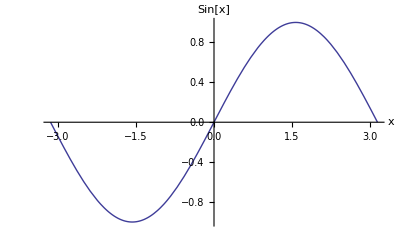

```mathematica
Plot[Sin[x], {x, -π, π}, AxesLabel -> { "x", "Sin[x]"}]
```

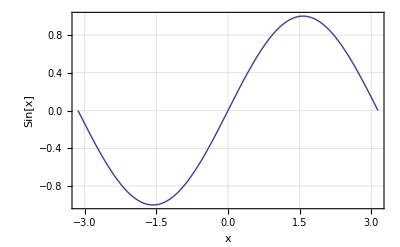

```mathematica
Plot[Sin[x],{x,-π,π},AxesLabel->{Style["x",FontWeight->"Bold",FontFamily->"Tekton"],Style["Sin[x]",FontWeight->"Bold",FontFamily->"Tekton"]},Frame->True,GridLines->Automatic,AxesStyle->{RGBColor[1,0,0],Thickness[0.01]},BaseStyle->{FontSlant->"Italic",FontSize->12}]
```

```mathematica
Plot3D[Sin[x] Cos[y],{x,-π,π},{y,-2 π,2 π},AxesLabel->{"x","y","z"},PlotPoints->35,BaseStyle->{FontSlant->"Italic",FontSize->12}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{2 Sin[t],5 Cos[t],t},{t,0,4 π},BaseStyle->Hue[0.4],Axes->False]
```

-Graphics3D-

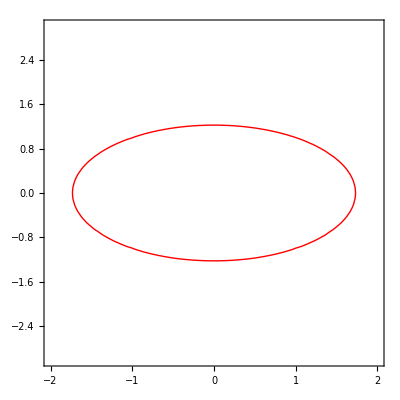

```mathematica
pl1=ContourPlot[x^2+2 y^2==3,{x,-2,2},{y,-3,3},ContourStyle->{RGBColor[1,0,0]}]
```

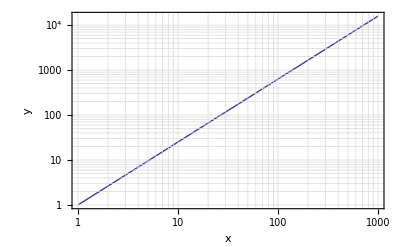

```mathematica
LogLogPlot[x^1.4,{x,1,1000},FrameLabel->{"x","y"},GridLines->Automatic,Frame->True]
```

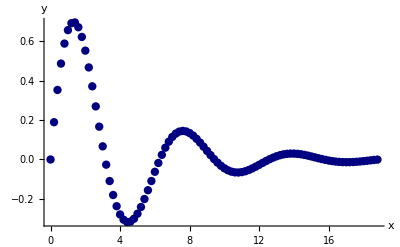

```mathematica
tab1=Table[{x,Sin[x] ⅇ^(-x/4)},{x,0,6 π,0.2}];
ListPlot[tab1,PlotStyle->{RGBColor[0,0,0.500008],PointSize[0.015]},AxesLabel->{"x","y"},PlotRange->All]
```

```mathematica
<<"ErrorBarPlots`";<<"PlotLegends`"
```

```mathematica
tab2=Table[{x,Sin[x] ⅇ^(-x/8)},{x,0,6 π,0.2}];
```

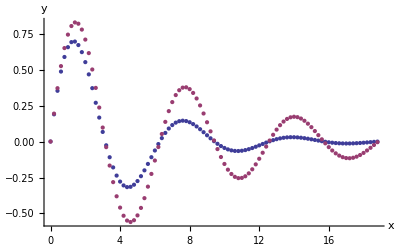

```mathematica
ListPlot[{tab1,tab2},AxesLabel->{"x","y"},PlotRange->All]
```

```mathematica
pl1=ContourPlot[x^2+2 y^2==3,{x,-2,2},{y,-2,2},ContourStyle->{RGBColor[1,0,0]},AspectRatio->1];
pl2=Animate[Show[pl1,Graphics[Disk[{√3 Sin[x], √(3/2)Cos[x]},0.1]],PlotRange->{{-2,2},{-2,2}},AspectRatio->1],{x,0,2 π}, ContentSize-> Full]
```

```mathematica
Disk[{√3 Sin[x], √(3/2)Cos[x]},0.1]
```

Disk[{√3 sin(x),√(3/2) cos(x)},0.1]

```mathematica
?Disk
```

RowBox[{"Disk", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"]}], "}"}], ",", StyleBox["r", "TI"]}], "]"}] is a two-dimensional graphics primitive that represents a filled disk of radius StyleBox["r", "TI"] centered at the point StyleBox["x", "TI"], StyleBox["y", "TI"]. 
RowBox[{"Disk", "[", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"]}], "}"}], "]"}] gives a disk of radius 1. 
RowBox[{"Disk", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"]}], "}"}], ",", StyleBox["r", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["θ", "TR"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["θ", "TR"], StyleBox["2", "TR"]]}], "}"}]}], "]"}] gives a segment of a disk. 
RowBox[{"Disk", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["r", "TI"], StyleBox["x", "TI"]], ",", SubscriptBox[StyleBox["r", "TI"], StyleBox["y", "TI"]]}], "}"}]}], "]"}] gives an elliptical disk with semi-axes of lengths SubscriptBox[StyleBox["r", "TI"], StyleBox["x", "TI"]] and SubscriptBox[StyleBox["r", "TI"], StyleBox["y", "TI"]], oriented parallel to the coordinate axes.

General::obspkg: TraditionalForm`"Graphics`Arrow`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

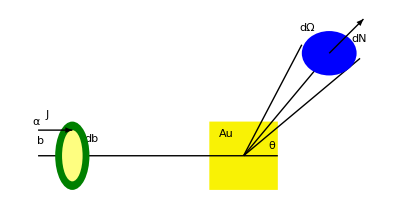

```mathematica
Show[Graphics[{{RGBColor[0.976577,0.949233,0.0195315],Rectangle[{-2,-2},{2,2}]},Line[{{0,0},{-12,0}}],Line[{{0,0},{5,6}}],Line[{{0,0},{2,0}}],Line[{{0,0},{3.4,6.5}}],Line[{{0,0},{6.8,5.7}}],{RGBColor[0,0.500008,0],Disk[{-10,0},{1,2}]},{RGBColor[0.996109,0.996109,0.500008],Disk[{-10,0},{.6,1.5}]},{RGBColor[0,0,0.996109],Disk[{5,6},{1.6,1.3}]},Arrow[{{-12,1.5},{-10,1.5}}],Arrow[{{5,6},{7,8}}],Text["b",{-11.88,0.857724}],Text["J",{-11.4616,2.392}],Text["Au",{-1.00059,1.27616}],Text["dN",{6.74052,6.85534}],Text["dΩ",{3.74171,7.483}],Text["θ",{1.64952,0.578765}],Text["db",{-8.88118,0.997203}],Text["α",{-12.0892,1.97356}]},AspectRatio->Automatic]]
```

```mathematica
poly=Cos[x]∑_(n=0)^∞ a[n] x^n + Sin[x] ∑_(n=0)^∞ b[n] x^n
```

cos(x) ∑_(n=0)^∞ a(n) x^n+sin(x) ∑_(n=0)^∞ b(n) x^n

```mathematica
listf={Cos[x], Sin[x]}
```

{cos(x),sin(x)}

```mathematica
AppendTo[listf, listf[[1]] ∫(listf[[2]]/listf[[1]])^2 ⅆx]//Simplify
```

{cos(x),sin(x),sin(x)-x cos(x)}

```mathematica
AppendTo[listf, listf[[2]] ∫(listf[[3]]/listf[[2]])^2 ⅆx]//Simplify
```

{cos(x),sin(x),sin(x)-x cos(x),-1/3 x sin(x) (x^2+3 x cot(x)-3)}

```mathematica
AppendTo[listf, listf[[3]] ∫(listf[[4]]/listf[[3]])^2 ⅆx]//Simplify
```

{cos(x),sin(x),sin(x)-x cos(x),-1/3 x sin(x) (x^2+3 x cot(x)-3),1/45 x^3 (3 (5-2 x^2) sin(x)+x (x^2-15) cos(x))}

```mathematica
poly=Apply[Plus,listf]//Simplify
```

(-(2 x^5)/15+x+2) sin(x)+(x^6/45-x^4/3-x^2-x+1) cos(x)

```mathematica
Coefficient[poly,Cos[x]]
```

x^6/45-x^4/3-x^2-x+1

```mathematica
Coefficient[poly,Sin[x]]
```

-(2 x^5)/15+x+2

```mathematica
Iterate[initial_List,maxn_]:=Module[(*---local variables---*){df={},dfh,f=initial,fh},(*---iterate the formula and collect the results---*)Do[AppendTo[f,f[[n]] Integrate[(f[[n+1]]/f[[n]])^2,x]],{n,1,maxn}];
(*---calculate the sum of all elements in f---*)f=Expand[Apply[Plus,Simplify[f]]];
(*---extract the coefficients from the polynom---*)fh={Coefficient[f,initial[[1]]]};
AppendTo[fh,Coefficient[f,initial[[2]]]];
(*---return the result---*)fh]
```

```mathematica
Iterate[{Cos[x],Sin[x]},4]
```

{(2 x^9)/945-x^7/45+x^6/45-x^4/3-x^2-x+1,x^10/4725-x^8/105+x^6/45-(2 x^5)/15+x+2}

```mathematica
Iterator[{expr1_,expr2_}]:=Expand[expr1 Integrate[(expr2 / expr1)^2,x]]
```

```mathematica
takeLastTwoElemets[l_List]:=Take[l,-2]
```

```mathematica
Iterate1[input_,n_]:=Block[{F=input,t1},t1=Apply[Plus,Flatten[Simplify[Last[Table[Flatten[AppendTo[F,Expand[Apply[Iterator[takeLastTwoElemets[#]]&,{Flatten[F]}]]]],{n}]]]]];
Map[Coefficient[t1,#]&,input]]
```

```mathematica
Iterate1[{Cos[x],Sin[x]},5]//Timing
```

{0.452,{-x^15/4465125+x^13/42525-x^11/4725+(2 x^9)/945-x^7/45+x^6/45-x^4/3-x^2-x+1,x^14/297675-(4 x^12)/42525+(2 x^10)/4725-x^8/105+x^6/45-(2 x^5)/15+x+2}}

```mathematica
Iterate[{Sinh[x],Cosh[x]},3]
```

{x^6/45+x^4/3-x^2+x+1,x-(2 x^5)/15}

```mathematica
A=({{2, 4}, {-5, 1}})
```

(2 | 4
-5 | 1)

```mathematica
B = ({{5, 2}, {9, -4}})
```

(5 | 2
9 | -4)

```mathematica
A.B
```

(46 | -12
-16 | -14)

```mathematica
l=({{Subscript[λ, 11], Subscript[λ, 12]}, {Subscript[λ, 21], Subscript[λ, 22]}})
```

(λ_11 | λ_12
λ_21 | λ_22)

```mathematica
l.B
```

(5 λ_11+9 λ_12 | 2 λ_11-4 λ_12
5 λ_21+9 λ_22 | 2 λ_21-4 λ_22)

```mathematica
B.A
```

(0 | 22
38 | 32)

```mathematica
l=({{Subscript[λ, 11], Subscript[λ, 12], Subscript[λ, 13]}, {Subscript[λ, 21], Subscript[λ, 22], Subscript[λ, 23]}, {Subscript[λ, 31], Subscript[λ, 32], Subscript[λ, 33]}})
```

(λ_11 | λ_12 | λ_13
λ_21 | λ_22 | λ_23
λ_31 | λ_32 | λ_33)

```mathematica
Transpose[mm]
```

Transpose[mm]

```mathematica
Transpose[l]
```

(λ_11 | λ_21 | λ_31
λ_12 | λ_22 | λ_32
λ_13 | λ_23 | λ_33)

```mathematica
IdentityMatrix[3]
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
IdentityMatrix[3].l
```

(λ_11 | λ_12 | λ_13
λ_21 | λ_22 | λ_23
λ_31 | λ_32 | λ_33)

```mathematica
Transpose[l].IdentityMatrix[3]
```

(λ_11 | λ_21 | λ_31
λ_12 | λ_22 | λ_32
λ_13 | λ_23 | λ_33)

```mathematica
IdentityMatrix[3].Transpose[l]
```

(λ_11 | λ_21 | λ_31
λ_12 | λ_22 | λ_32
λ_13 | λ_23 | λ_33)

```mathematica
Inverse[l]
```

((λ_22 λ_33-λ_23 λ_32)/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33) | (λ_13 λ_32-λ_12 λ_33)/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33) | (λ_12 λ_23-λ_13 λ_22)/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33)
(λ_23 λ_31-λ_21 λ_33)/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33) | (λ_11 λ_33-λ_13 λ_31)/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33) | (λ_13 λ_21-λ_11 λ_23)/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33)
(λ_21 λ_32-λ_22 λ_31)/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33) | (λ_12 λ_31-λ_11 λ_32)/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33) | (λ_11 λ_22-λ_12 λ_21)/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33))

```mathematica
Inverse[mm]
```

mm

```mathematica
l.Inverse[l]//Simplify
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
R=({{Cos[ϕ], Sin[ϕ]}, {-Sin[ϕ], Cos[ϕ]}})(*---2x 2 rotation matrices ---*)
```

(cos(ϕ) | sin(ϕ)
-sin(ϕ) | cos(ϕ))

```mathematica
Inverse[R]//Simplify
```

(cos(ϕ) | -sin(ϕ)
sin(ϕ) | cos(ϕ))

```mathematica
Transpose[R]
```

(cos(ϕ) | -sin(ϕ)
sin(ϕ) | cos(ϕ))

```mathematica
R.Inverse[R]//Simplify
```

(1 | 0
0 | 1)

```mathematica
R.Transpose[R]//Simplify
```

(1 | 0
0 | 1)

```mathematica
x1=({{1}, {0}, {0}})
```

(1
0
0)

```mathematica
Subscript[λ, Subscript[x, 3]]=({{0, 1, 0}, {-1, 0, 0}, {0, 0, 1}})
```

(0 | 1 | 0
-1 | 0 | 0
0 | 0 | 1)

```mathematica
X1t=Subscript[λ, Subscript[x, 3]].x1
```

(0
-1
0)

```mathematica
Subscript[λ, Subscript[x, 3]].({{a}, {b}, {c}})
```

(b
-a
c)

```mathematica
x2=({{0}, {1}, {0}})
```

(0
1
0)

```mathematica
x2t=Subscript[λ, Subscript[x, 3]].x2
```

(1
0
0)

```mathematica
x3=({{0}, {0}, {1}})
```

(0
0
1)

```mathematica
x3t=Subscript[λ, Subscript[x, 3]].x3
```

(0
0
1)

```mathematica
Subscript[λ, Subscript[x, 1]]=({{1, 0, 0}, {0, 0, 1}, {0, -1, 0}})
```

(1 | 0 | 0
0 | 0 | 1
0 | -1 | 0)

```mathematica
x⃗=({{Subscript[x, 1]}, {Subscript[x, 2]}, {Subscript[x, 3]}})
```

(x_1
x_2
x_3)

```mathematica
OverVector[xh] = Subscript[λ, Subscript[x, 3]].x⃗
```

(x_2
-x_1
x_3)

```mathematica
OverVector[xf]=Subscript[λ, Subscript[x, 1]].OverVector[xh]
```

(x_2
x_3
x_1)

```mathematica
Subscript[λ, Subscript[x, 1]].Subscript[λ, Subscript[x, 3]].x⃗
```

(x_2
x_3
x_1)

```mathematica
Subscript[λ, Subscript[x, 2]]=Subscript[λ, Subscript[x, 1]].Subscript[λ, Subscript[x, 3]]
```

(0 | 1 | 0
0 | 0 | 1
1 | 0 | 0)

```mathematica
Subscript[λ, Subscript[x, 2]].x⃗
```

(x_2
x_3
x_1)

```mathematica
Subscript[λ, Subscript[x, 3]].Subscript[λ, Subscript[x, 1]] ≠Subscript[λ, Subscript[x, 1]].Subscript[λ, Subscript[x, 3]]
```

True

```mathematica
Subscript[R, Subscript[x, 3]][ϕ_]:=({{Cos[ϕ], Sin[ϕ], 0}, {-Sin[ϕ], Cos[ϕ], 0}, {0, 0, 1}})
```

R[ϕ_][i][j]:=Cos[i⃗,j⃗]

```mathematica
rh=Subscript[R, Subscript[x, 3]][ϕ].x⃗
```

(cos(ϕ) x_1+sin(ϕ) x_2
cos(ϕ) x_2-sin(ϕ) x_1
x_3)

```mathematica
ListAnimate[Map[(Show[Graphics3D[{
Arrow[{{0,0,0},{0,0,3}}],
RGBColor[0,0,0.996109],
Line[{{0,0,0},rh//Flatten}] /.{Subscript[x, 1] ->  1,Subscript[x, 2] -> 0,Subscript[x, 3] ->  0,ϕ->#}}],Axes->True, AxesLabel->{"x1", "x2", "x3"}, PlotRange ->  {{-1.5,1.5},{-1.5,1.5},{0,1.5}}])&,Table[i,{i,0,2 π,.3}]]]
```

```mathematica
Subscript[R, Subscript[x, 2]][θ_]:=({{Cos[θ], 0, -Sin[θ]}, {0, 1, 0}, {Sin[θ], 0, Cos[θ]}})
```

```mathematica
x2r = Subscript[R, Subscript[x, 2]][θ].x⃗
```

(cos(θ) x_1-sin(θ) x_3
x_2
sin(θ) x_1+cos(θ) x_3)

```mathematica
ListAnimate[Map[(Show[Graphics3D[{
Line[{{0,0,0},{0,3,0}}],
RGBColor[0,0,0.996109],
Line[{{0,0,0},x2r//Flatten}] /.{Subscript[x, 1] ->  1,Subscript[x, 2] -> 0,Subscript[x, 3] ->  0,θ->#}}],Axes->True, AxesLabel->{"x1", "x2", "x3"},                              PlotRange ->  {{-1.5,1.5},{0,1.5},{-1.5,1.5}}])&,Table[i,{i,0,2 π,.3}]]]
```

```mathematica
genRot= Subscript[R, Subscript[x, 3]][ψ].Subscript[R, Subscript[x, 2]][θ].Subscript[R, Subscript[x, 3]][ϕ]//Simplify
```

(cos(θ) cos(ϕ) cos(ψ)-sin(ϕ) sin(ψ) | cos(θ) cos(ψ) sin(ϕ)+cos(ϕ) sin(ψ) | -cos(ψ) sin(θ)
-cos(ψ) sin(ϕ)-cos(θ) cos(ϕ) sin(ψ) | cos(ϕ) cos(ψ)-cos(θ) sin(ϕ) sin(ψ) | sin(θ) sin(ψ)
cos(ϕ) sin(θ) | sin(θ) sin(ϕ) | cos(θ))

```mathematica
genRot.x⃗
```

((cos(θ) cos(ϕ) cos(ψ)-sin(ϕ) sin(ψ)) x_1+(cos(θ) cos(ψ) sin(ϕ)+cos(ϕ) sin(ψ)) x_2-cos(ψ) sin(θ) x_3
(-cos(ψ) sin(ϕ)-cos(θ) cos(ϕ) sin(ψ)) x_1+(cos(ϕ) cos(ψ)-cos(θ) sin(ϕ) sin(ψ)) x_2+sin(θ) sin(ψ) x_3
cos(ϕ) sin(θ) x_1+sin(θ) sin(ϕ) x_2+cos(θ) x_3)

```mathematica
genRot.x⃗ x2//Flatten
```

{0,x_3 sin(θ) sin(ψ)+x_1 (-cos(θ) sin(ψ) cos(ϕ)-cos(ψ) sin(ϕ))+x_2 (cos(ψ) cos(ϕ)-cos(θ) sin(ψ) sin(ϕ)),0}

```mathematica
Subscript[ϕ, 0]=π/3;
Subscript[θ, 0]=π/4;
r323x=genRot.x⃗//Flatten;
ListAnimate[Map[(Show[Graphics3D[{
Arrow[{{-3,0,0},{3,0,0}}],
Arrow[{{0,-3,0},{0,3,0}}],
Arrow[{{0,0,-3},{0,0,3}}],
Line[{Flatten[r323x (x1)],Flatten[r323x (x1+x2)]}] /.{Subscript[x, 1] ->  1,Subscript[x, 2] -> 0,Subscript[x, 3] ->  0,ϕ->Subscript[ϕ, 0],θ->Subscript[θ, 0],ψ->#},
Line[{Flatten[r323x (x2)],Flatten[r323x (x2+x3)]}] /.{Subscript[x, 1] ->  1,Subscript[x, 2] -> 0,Subscript[x, 3] ->  0,ϕ->Subscript[ϕ, 0],θ->Subscript[θ, 0],ψ->#},
Line[{Flatten[r323x (x3)],Flatten[r323x (x3+x1)]}] /.{Subscript[x, 1] ->  1,Subscript[x, 2] -> 0,Subscript[x, 3] ->  0,ϕ->Subscript[ϕ, 0],θ->Subscript[θ, 0],ψ->#},
Line[{Flatten[r323x (x1)],Flatten[r323x (x1+x3)]}] /.{Subscript[x, 1] ->  1,Subscript[x, 2] -> 0,Subscript[x, 3] ->  0,ϕ->Subscript[ϕ, 0],θ->Subscript[θ, 0],ψ->#},
Line[{Flatten[r323x (x2)],Flatten[r323x (x2+x1)]}] /.{Subscript[x, 1] ->  1,Subscript[x, 2] -> 0,Subscript[x, 3] ->  0,ϕ->Subscript[ϕ, 0],θ->Subscript[θ, 0],ψ->#},
Line[{Flatten[r323x (x3)],Flatten[r323x (x3+x2)]}] /.{Subscript[x, 1] ->  1,Subscript[x, 2] -> 0,Subscript[x, 3] ->  0,ϕ->Subscript[ϕ, 0],θ->Subscript[θ, 0],ψ->#},
Line[{Flatten[r323x (x2+x3)],r323x}] /.{Subscript[x, 1] ->  1,Subscript[x, 2] -> 0,Subscript[x, 3] ->  0,ϕ->Subscript[ϕ, 0],θ->Subscript[θ, 0],ψ->#},
Line[{Flatten[r323x (x3+x1)],r323x}] /.{Subscript[x, 1] ->  1,Subscript[x, 2] -> 0,Subscript[x, 3] ->  0,ϕ->Subscript[ϕ, 0],θ->Subscript[θ, 0],ψ->#} ,
Line[{Flatten[r323x (x1+x2)],r323x}] /.{Subscript[x, 1] ->  1,Subscript[x, 2] -> 0,Subscript[x, 3] ->  0,ϕ->Subscript[ϕ, 0],θ->Subscript[θ, 0],ψ->#},
RGBColor[0,0,0.996109],
Arrow[{{0,0,0},r323x}] /.{Subscript[x, 1] ->  1,Subscript[x, 2] -> 0,Subscript[x, 3] ->0,ϕ->Subscript[ϕ, 0],θ->Subscript[θ, 0],ψ->#}}],
Axes->True, AxesLabel->{"x1", "x2", "x3"},                              PlotRange ->  {{-1.5,1.5},{-1.5,1.5},{-1.5,1.5}}])&,Table[i,{i,0,2 π,.3}]]]
```

```mathematica
Subscript[ϕ, 0]=π/3;
Subscript[θ, 0]=π/4;
r323x=genRot.x⃗//Flatten;
ListAnimate[Map[(Show[Graphics3D[{
Arrow[{{-3,0,0},{3,0,0}}],
Arrow[{{0,-3,0},{0,3,0}}],
Arrow[{{0,0,-3},{0,0,3}}],
Line[{Flatten[r323x (x2+x3)],r323x}] /.{Subscript[x, 1] ->  1,Subscript[x, 2] -> 0,Subscript[x, 3] ->  0,ϕ->Subscript[ϕ, 0],θ->Subscript[θ, 0],ψ->#},
Line[{Flatten[r323x (x3+x1)],r323x}] /.{Subscript[x, 1] ->  1,Subscript[x, 2] -> 0,Subscript[x, 3] ->  0,ϕ->Subscript[ϕ, 0],θ->Subscript[θ, 0],ψ->#} ,
Line[{Flatten[r323x (x1+x2)],r323x}] /.{Subscript[x, 1] ->  1,Subscript[x, 2] -> 0,Subscript[x, 3] ->  0,ϕ->Subscript[ϕ, 0],θ->Subscript[θ, 0],ψ->#},
RGBColor[0,0,0.996109],
Arrow[{{0,0,0},r323x}] /.{Subscript[x, 1] ->  1,Subscript[x, 2] -> 0,Subscript[x, 3] ->0,ϕ->Subscript[ϕ, 0],θ->Subscript[θ, 0],ψ->#}}],
Axes->True, AxesLabel->{"x1", "x2", "x3"},                              PlotRange ->  {{-1.5,1.5},{-1.5,1.5},{-1.5,1.5}}])&,Table[i,{i,0,2 π,.1}]]]
```

```mathematica
Needs["VectorAnalysis`"]
```

```mathematica
Clear[A,B]
```

```mathematica
C⃗=A⃗+B⃗
```

A⃗+B⃗

```mathematica
C⃗==A⃗+B⃗
```

True

```mathematica
T=({{-x y, -y^2}, {x^2, x y}})
```

(-x y | -y^2
x^2 | x y)

```mathematica
lam=({{Cos[θ], Sin[θ]}, {-Sin[θ], Cos[θ]}})
```

(cos(θ) | sin(θ)
-sin(θ) | cos(θ))

```mathematica
r⃗=Flatten[lam.({{x}, {y}})]
```

{x cos(θ)+y sin(θ),y cos(θ)-x sin(θ)}

```mathematica
-r⃗⟦1⟧r⃗⟦2⟧==∑_(k=1)^2 ∑_(l=1)^2 lam⟦1,k⟧lam⟦1,l⟧T⟦k,l⟧
```

(y cos(θ)-x sin(θ)) (-x cos(θ)-y sin(θ))==x^2 sin(θ) cos(θ)+x y sin^2(θ)-x y cos^2(θ)-y^2 sin(θ) cos(θ)

```mathematica
-r⃗⟦1⟧r⃗⟦2⟧==∑_(k=1)^2 ∑_(l=1)^2 lam⟦1,k⟧lam⟦1,l⟧T⟦k,l⟧//Simplify
```

True

```mathematica
C⃗.C⃗//Expand
```

(A⃗+B⃗).(A⃗+B⃗)

```mathematica
DotProduct[C⃗,C⃗]//Expand
```

DotProduct(A⃗+B⃗,A⃗+B⃗)

```mathematica
A⃗.B⃗==1/2(-A^2-B^2+C^2)
```

A⃗.B⃗==1/2 (-A^2-B^2+C^2)

```mathematica
A⃗.B⃗==1/2(-A^2-B^2+C^2)//Simplify
```

A^2+2 A⃗.B⃗+B^2==C^2

```mathematica
(A⃗-B⃗).(A⃗+B⃗)//Simplify
```

(A⃗-B⃗).(A⃗+B⃗)

```mathematica
C⃗=A⃗×B⃗
```

A⃗×B⃗

```mathematica
A⃗.(A⃗×B⃗)//Simplify
```

A⃗.A⃗×B⃗

```mathematica
A⃗×B⃗ == - B⃗ ×A⃗ //Simplify
```

A⃗×B⃗+B⃗×A⃗==0

```mathematica
A⃗×(B⃗×C⃗ )≠(A⃗×B⃗)×C⃗
```

A⃗×(B⃗×C⃗)≠(A⃗×B⃗)×C⃗

```mathematica
A⃗×(B⃗×C⃗ )
```

A⃗×(B⃗×C⃗)

```mathematica
A⃗×(B⃗×C⃗ )==A⃗.C⃗ B⃗ -A⃗.B⃗ C⃗
```

A⃗×(B⃗×C⃗)==B⃗ A⃗.C⃗-C⃗ A⃗.B⃗

```mathematica
(A⃗×B⃗).(C⃗×D⃗ )==A⃗.C⃗ B⃗.D⃗ -A⃗.D⃗ B⃗.C⃗
```

A⃗×B⃗.C⃗×D⃗==A⃗.C⃗ B⃗.D⃗-A⃗.D⃗ B⃗.C⃗

```mathematica
A⃗.(B⃗×C⃗)==(B⃗×C⃗).A⃗
```

A⃗.B⃗×C⃗==B⃗×C⃗.A⃗

```mathematica
(A⃗×B⃗)×(C⃗×D⃗ )==A⃗×(B⃗.D⃗)C⃗-A⃗×(B⃗.C⃗)D⃗
```

(A⃗×B⃗)×(C⃗×D⃗)==C⃗ A⃗×(B⃗.D⃗)-D⃗ A⃗×(B⃗.C⃗)

```mathematica
(A⃗×B⃗).(A⃗×B⃗)==(A⃗)^2(B⃗)^2-(A⃗.B⃗)^2
```

A⃗×B⃗.A⃗×B⃗==(A⃗)^2 (B⃗)^2-(A⃗.B⃗)^2

```mathematica
A⃗×(B⃗×C⃗)+B⃗×(C⃗×A⃗)+C⃗×(A⃗×B⃗)==0//Simplify
```

A⃗×(B⃗×C⃗)+B⃗×(C⃗×A⃗)+C⃗×(A⃗×B⃗)==0

```mathematica
(A⃗-B⃗)×(A⃗+B⃗)==2 A⃗×B⃗
```

(A⃗-B⃗)×(A⃗+B⃗)==2 A⃗×B⃗

```mathematica
Nabla[ϕ ψ]== ψ∇ϕ + ϕ ∇ψ
```

Nabla(ψ ϕ)==ψ ∇ϕ+ϕ ∇ψ

```mathematica
Clear[S]
```

```mathematica
S=(x^2+y^2+z^2)^(-3/2)
```

1/((x^2+y^2+z^2)^(3/2))

```mathematica
gr=Grad[S]
```

{0,0,0}

```mathematica
gr =∇S
```

∇1/((x^2+y^2+z^2)^(3/2))

```mathematica
Needs["VectorAnalysis`"]
```

```mathematica
SetCoordinates[Cartesian[x,y,z]]
```

Cartesian(x,y,z)

```mathematica
Clear[x,y,z]
```

```mathematica
S=(x^2+y^2+z^2)^(-3/2)
```

1/((x^2+y^2+z^2)^(3/2))

```mathematica
{D[S, x],D[S, y],D[S, z]}
```

{-(3 x)/((x^2+y^2+z^2)^(5/2)),-(3 y)/((x^2+y^2+z^2)^(5/2)),-(3 z)/((x^2+y^2+z^2)^(5/2))}

```mathematica
gr=Grad[S]
```

{-(3 x)/((x^2+y^2+z^2)^(5/2)),-(3 y)/((x^2+y^2+z^2)^(5/2)),-(3 z)/((x^2+y^2+z^2)^(5/2))}

```mathematica
∇S
```

∇1/((x^2+y^2+z^2)^(3/2))

```mathematica
di = Div[gr]//Simplify
```

6/((x^2+y^2+z^2)^(5/2))

```mathematica
Nabla[]
```

Nabla()

```mathematica
Curl[gr]//MatrixForm
```

(0
0
0)

```mathematica
polar={x[t]==r[t] Cos[θ[t]],y[t]==r[t] Sin[θ[t]]};TableForm[polar]
```

x(t)==r(t) cos(θ(t))
y(t)==r(t) sin(θ(t))

```mathematica
velocity = D[polar, t];TableForm[velocity]
```

x'(t)==r'(t) cos(θ(t))-r(t) θ'(t) sin(θ(t))
y'(t)==r'(t) sin(θ(t))+r(t) θ'(t) cos(θ(t))

```mathematica
Solve[polar,{r[t],θ[t]}]
```

Solve::ifun: Inverse functions are being used by TraditionalForm`Solve, so some solutions may not be found; use Reduce for complete solution information.

{{r(t)→-(x(t))^2/(√((x(t))^2+(y(t))^2))-(y(t))^2/(√((x(t))^2+(y(t))^2)),θ(t)→-cos^-1(-(x(t))/(√((x(t))^2+(y(t))^2)))},{r(t)→-(x(t))^2/(√((x(t))^2+(y(t))^2))-(y(t))^2/(√((x(t))^2+(y(t))^2)),θ(t)→cos^-1(-(x(t))/(√((x(t))^2+(y(t))^2)))},{r(t)→(x(t))^2/(√((x(t))^2+(y(t))^2))+(y(t))^2/(√((x(t))^2+(y(t))^2)),θ(t)→-cos^-1((x(t))/(√((x(t))^2+(y(t))^2)))},{r(t)→(x(t))^2/(√((x(t))^2+(y(t))^2))+(y(t))^2/(√((x(t))^2+(y(t))^2)),θ(t)→cos^-1((x(t))/(√((x(t))^2+(y(t))^2)))}}

```mathematica
Reduce[polar,{r[t],θ[t]}]
```

(c_1∈ℤ∧((y(t)≠0∧((x(t) √((x(t))^2+(y(t))^2)+(x(t))^2+(y(t))^2≠0∧r(t)==-√((x(t))^2+(y(t))^2)∧θ(t)==2 π c_1+2 tan^-1((-√((x(t))^2+(y(t))^2)-x(t))/(y(t))))∨(-x(t) √((x(t))^2+(y(t))^2)+(x(t))^2+(y(t))^2≠0∧r(t)==√((x(t))^2+(y(t))^2)∧θ(t)==2 π c_1+2 tan^-1((√((x(t))^2+(y(t))^2)-x(t))/(y(t))))))∨(x(t)≠0∧y(t)==0∧r(t)==x(t)∧θ(t)==2 π c_1)∨(y(t)==0∧r(t)==-x(t)∧θ(t)==2 π c_1+π)))∨((θ(t)-π)/(2 π)∉ℤ∧x(t)==0∧y(t)==0∧r(t)==0)

```mathematica
Solve[velocity,{r'[t],θ'[t]}]
```

{{r'(t)→-(-cos(θ(t)) x'(t)-sin(θ(t)) y'(t))/(sin^2(θ(t))+cos^2(θ(t))),θ'(t)→-(sin(θ(t)) x'(t)-cos(θ(t)) y'(t))/(r(t) (sin^2(θ(t))+cos^2(θ(t))))}}

```mathematica
result=Solve[velocity,{r'[t],θ'[t]}] /.Solve[polar,{r[t],θ[t]}]
```

Solve::ifun: Inverse functions are being used by TraditionalForm`Solve, so some solutions may not be found; use Reduce for complete solution information.

({ (r'(t)→-(x(t) x'(t))/(√((x(t))^2+(y(t))^2))-√(1-(x(t))^2/((x(t))^2+(y(t))^2)) y'(t)), (θ'(t)→-((x(t) y'(t))/(√((x(t))^2+(y(t))^2))-√(1-(x(t))^2/((x(t))^2+(y(t))^2)) x'(t))/(-(x(t))^2/(√((x(t))^2+(y(t))^2))-(y(t))^2/(√((x(t))^2+(y(t))^2))))}
{ (r'(t)→√(1-(x(t))^2/((x(t))^2+(y(t))^2)) y'(t)-(x(t) x'(t))/(√((x(t))^2+(y(t))^2))), (θ'(t)→-(√(1-(x(t))^2/((x(t))^2+(y(t))^2)) x'(t)+(x(t) y'(t))/(√((x(t))^2+(y(t))^2)))/(-(x(t))^2/(√((x(t))^2+(y(t))^2))-(y(t))^2/(√((x(t))^2+(y(t))^2))))}
{ (r'(t)→(x(t) x'(t))/(√((x(t))^2+(y(t))^2))-√(1-(x(t))^2/((x(t))^2+(y(t))^2)) y'(t)), (θ'(t)→-(-√(1-(x(t))^2/((x(t))^2+(y(t))^2)) x'(t)-(x(t) y'(t))/(√((x(t))^2+(y(t))^2)))/((x(t))^2/(√((x(t))^2+(y(t))^2))+(y(t))^2/(√((x(t))^2+(y(t))^2))))}
{ (r'(t)→(x(t) x'(t))/(√((x(t))^2+(y(t))^2))+√(1-(x(t))^2/((x(t))^2+(y(t))^2)) y'(t)), (θ'(t)→-(√(1-(x(t))^2/((x(t))^2+(y(t))^2)) x'(t)-(x(t) y'(t))/(√((x(t))^2+(y(t))^2)))/((x(t))^2/(√((x(t))^2+(y(t))^2))+(y(t))^2/(√((x(t))^2+(y(t))^2))))})

```mathematica
result=Solve[velocity,{r'[t],θ'[t]}] /.Solve[polar,{r[t],θ[t]}]⟦4⟧
```

Solve::ifun: Inverse functions are being used by TraditionalForm`Solve, so some solutions may not be found; use Reduce for complete solution information.

( (r'(t)→(x(t) x'(t))/(√((x(t))^2+(y(t))^2))+√(1-(x(t))^2/((x(t))^2+(y(t))^2)) y'(t)) |  (θ'(t)→-(√(1-(x(t))^2/((x(t))^2+(y(t))^2)) x'(t)-(x(t) y'(t))/(√((x(t))^2+(y(t))^2)))/((x(t))^2/(√((x(t))^2+(y(t))^2))+(y(t))^2/(√((x(t))^2+(y(t))^2)))))

```mathematica
Simplify[PowerExpand[FunctionExpand[result]]]
```

( (r'(t)→(x(t) x'(t)+y(t) y'(t))/(√((x(t))^2+(y(t))^2))) |  (θ'(t)→(x(t) y'(t)-y(t) x'(t))/((x(t))^2+(y(t))^2)))

```mathematica
TableForm[Flatten[Simplify[PowerExpand[FunctionExpand[result]]]]]
```

 (r'(t)→(x(t) x'(t)+y(t) y'(t))/(√((x(t))^2+(y(t))^2)))
 (θ'(t)→(x(t) y'(t)-y(t) x'(t))/((x(t))^2+(y(t))^2))

```mathematica
spherical={x[t]==r[t] Sin[θ[t]] Cos[ϕ[t]],y[t]==r[t] Sin[θ[t]] Sin[ϕ[t]],z[t]==r[t] Cos[θ[t]]};TableForm[spherical]
```

x(t)==r(t) sin(θ(t)) cos(ϕ(t))
y(t)==r(t) sin(θ(t)) sin(ϕ(t))
z(t)==r(t) cos(θ(t))

```mathematica
θ[t] = π/6 t;
ϕ[t] = π/3 t;
r[t] = 1;
r⃗ = {x[t], y[t], z[t]} /. Solve[spherical, {x[t], y[t], z[t]}][[1]];
ListAnimate[Map[(Show[Graphics3D[{
       Arrow[{{-3, 0, 0}, {3, 0, 0}}],
       Arrow[{{0, -3, 0}, {0, 3, 0}}],
       Arrow[{{0, 0, -3}, {0, 0, 3}}],
       Line[{{r⃗[[1]], r⃗[[2]], 0},r⃗}] /. { t -> #},
       Line[{{0, r⃗[[2]], r⃗[[3]]}, r⃗}] /. { t -> #},
       Line[{{r⃗[[1]], 0, r⃗[[3]]}, r⃗}] /. { t -> #},
       Line[{{r⃗[[1]], 0, 0}, {r⃗[[1]], r⃗[[2]], 0}}] /. { t -> #},
       Line[{{r⃗[[1]], 0, 0}, {r⃗[[1]], 0, r⃗[[3]]}}] /. { t -> #},
       Line[{{0, r⃗[[2]], 0}, {r⃗[[1]], r⃗[[2]], 0}}] /. { t -> #},
       Line[{{0, r⃗[[2]], 0}, {0, r⃗[[2]], r⃗[[3]]}}] /. { t -> #},
       Line[{{0, 0, r⃗[[3]]}, {r⃗[[1]], 0, r⃗[[3]]}}] /. { t -> #},
       Line[{{0, 0, r⃗[[3]]}, {0, r⃗[[2]], r⃗[[3]]}}] /. { t -> #},
       RGBColor[0, 0, 0.996109],
 Arrow[{{0, 0, 0},r⃗}] /. { t -> #}}],
     Axes -> True, AxesLabel -> {"x1", "x2","x3"},                              
     PlotRange ->  {{-1.5, 1.5}, {-1.5, 1.5}, {-1.5, 1.5}}]) &, 
  Table[i, {i, 0,30, .1}]]]
```

```mathematica
θ[t] = π/6 t;
ϕ[t] = π/3 ;
r[t] = 1;
r⃗ = {x[t], y[t], z[t]} /. Solve[spherical, {x[t], y[t], z[t]}][[1]];
ListAnimate[Map[(Show[ParametricPlot3D[r⃗ ,{t,-0.1,#}],
Graphics3D[{
       Arrow[{{-3, 0, 0}, {3, 0, 0}}],
       Arrow[{{0, -3, 0}, {0, 3, 0}}],
       Arrow[{{0, 0, -3}, {0, 0, 3}}],
       Line[{{r⃗[[1]], r⃗[[2]], 0},r⃗}] /. { t -> #},
       Line[{{0, r⃗[[2]], r⃗[[3]]}, r⃗}] /. { t -> #},
       Line[{{r⃗[[1]], 0, r⃗[[3]]}, r⃗}] /. { t -> #},
       Line[{{r⃗[[1]], 0, 0}, {r⃗[[1]], r⃗[[2]], 0}}] /. { t -> #},
       Line[{{r⃗[[1]], 0, 0}, {r⃗[[1]], 0, r⃗[[3]]}}] /. { t -> #},
       Line[{{0, r⃗[[2]], 0}, {r⃗[[1]], r⃗[[2]], 0}}] /. { t -> #},
       Line[{{0, r⃗[[2]], 0}, {0, r⃗[[2]], r⃗[[3]]}}] /. { t -> #},
       Line[{{0, 0, r⃗[[3]]}, {r⃗[[1]], 0, r⃗[[3]]}}] /. { t -> #},
       Line[{{0, 0, r⃗[[3]]}, {0, r⃗[[2]], r⃗[[3]]}}] /. { t -> #},
       RGBColor[0, 0, 0.996109],
 Arrow[{{0, 0, 0},r⃗}] /. { t -> #}}],
     Axes -> True, AxesLabel -> {"x1", "x2","x3"},                              
     PlotRange ->  {{-1.5, 1.5}, {-1.5, 1.5}, {-1.5, 1.5}}]) &, 
  Table[i, {i, 0,30, .1}]]]
```

```mathematica
Clear[R,θ]
```

```mathematica
R[θ_]:= ({{Cos[θ], -Sin[θ]}, {Sin[θ], Cos[θ]}})
```

```mathematica
R[π/8]
```

(cos(π/8) | -sin(π/8)
sin(π/8) | cos(π/8))

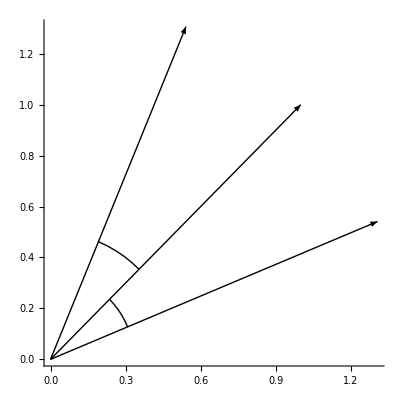

```mathematica
Show[Graphics[{Arrow[{{0,0}, {1,1}}],Arrow[{{0,0}, R[π/8].{1,1}}],
Circle[{0,0},1/2,{π/4,π/4+π/8}],
Arrow[{{0,0}, R[-π/8].{1,1}}],
Circle[{0,0},1/3,{π/4,π/4-π/8}]},
Axes -> True]]
```

```mathematica
ChemicalData["Caffeine","SpaceFillingMoleculePlot"]
```

-Graphics3D-

```mathematica
ChemicalData["Caffeine","Properties"]
```

{AcidityConstant,AcidityConstants,AdjacencyMatrix,AlternateNames,AtomPositions,AutoignitionPoint,BeilsteinNumber,BoilingPoint,BondTally,CASNumber,CHColorStructureDiagram,CHStructureDiagram,CIDNumber,Codons,ColorStructureDiagram,CombustionHeat,CompoundFormulaDisplay,CompoundFormulaString,CriticalPressure,CriticalTemperature,Density,DensityGramsPerCC,DielectricConstant,DOTHazardClass,DOTNumbers,EdgeRules,EdgeTypes,EGECNumber,ElementMassFraction,ElementTally,ElementTypes,EUNumber,FlashPoint,FlashPointFahrenheit,FormalCharges,FormattedName,GmelinNumber,HBondAcceptorCount,HBondDonorCount,HenryLawConstant,HildebrandSolubility,HildebrandSolubilitySI,InChI,IonEquivalents,Ions,IonTally,IsoelectricPoint,IsomericSMILES,IUPACName,LogAcidityConstant,LowerExplosiveLimit,MDLNumber,MeltingBehavior,MeltingPoint,Memberships,MolarVolume,MolecularFormulaDisplay,MolecularFormulaString,MolecularWeight,MoleculePlot,Name,NFPAFireRating,NFPAHazards,NFPAHealthRating,NFPALabel,NFPAReactivityRating,NonHydrogenCount,NonStandardIsotopeCount,NonStandardIsotopeNumbers,NonStandardIsotopeTally,NSCNumber,OdorThreshold,OdorType,PartitionCoefficient,pH,Phase,RefractiveIndex,Resistivity,RotatableBondCount,RTECSClasses,RTECSNumber,SideChainAcidityConstant,SMILES,Solubility,SolubilityType,SpaceFillingMoleculePlot,StandardName,StructureDiagram,SurfaceTension,TautomerCount,ThermalConductivity,TopologicalPolarSurfaceArea,UpperExplosiveLimit,VanDerWaalsConstants,VaporDensity,VaporizationHeat,VaporPressure,VaporPressureTorr,VertexCoordinates,VertexTypes,Viscosity}

```mathematica
{"AcidityConstant","AcidityConstants","AdjacencyMatrix","AlternateNames","AtomPositions","AutoignitionPoint","BeilsteinNumber","BoilingPoint","BondTally","CASNumber","CHColorStructureDiagram","CHStructureDiagram","CIDNumber","Codons","ColorStructureDiagram","CombustionHeat","CompoundFormulaDisplay","CompoundFormulaString","CriticalPressure","CriticalTemperature","Density","DensityGramsPerCC","DielectricConstant","DOTHazardClass","DOTNumbers","EdgeRules","EdgeTypes","EGECNumber","ElementMassFraction","ElementTally","ElementTypes","EUNumber","FlashPoint","FlashPointFahrenheit","FormalCharges","FormattedName","GmelinNumber","HBondAcceptorCount","HBondDonorCount","HenryLawConstant","HildebrandSolubility","HildebrandSolubilitySI","InChI","IonEquivalents","Ions","IonTally","IsoelectricPoint","IsomericSMILES","IUPACName","LogAcidityConstant","LowerExplosiveLimit","MDLNumber","MeltingBehavior","MeltingPoint","Memberships","MolarVolume","MolecularFormulaDisplay","MolecularFormulaString","MolecularWeight","MoleculePlot","Name","NFPAFireRating","NFPAHazards","NFPAHealthRating","NFPALabel","NFPAReactivityRating","NonHydrogenCount","NonStandardIsotopeCount","NonStandardIsotopeNumbers","NonStandardIsotopeTally","NSCNumber","OdorThreshold","OdorType","PartitionCoefficient","pH","Phase","RefractiveIndex","Resistivity","RotatableBondCount","RTECSClasses","RTECSNumber","SideChainAcidityConstant","SMILES","Solubility","SolubilityType","SpaceFillingMoleculePlot","StandardName","StructureDiagram","SurfaceTension","TautomerCount","ThermalConductivity","TopologicalPolarSurfaceArea","UpperExplosiveLimit","VanDerWaalsConstants","VaporDensity","VaporizationHeat","VaporPressure","VaporPressureTorr","VertexCoordinates","VertexTypes","Viscosity"}
```

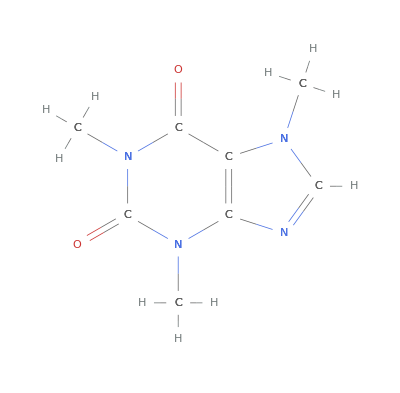

```mathematica
ChemicalData["Caffeine","CHColorStructureDiagram"]
```

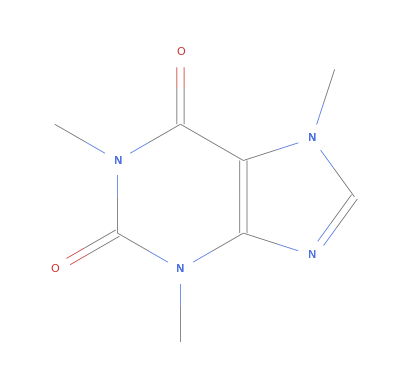

```mathematica
ChemicalData["Caffeine","ColorStructureDiagram"]
```

```mathematica
ChemicalData["Caffeine","CompoundFormulaDisplay"]
```

C_8H_10N_4O_2

```mathematica
ChemicalData["Caffeine","MolecularFormulaDisplay"]
```

C_8H_10N_4O_2

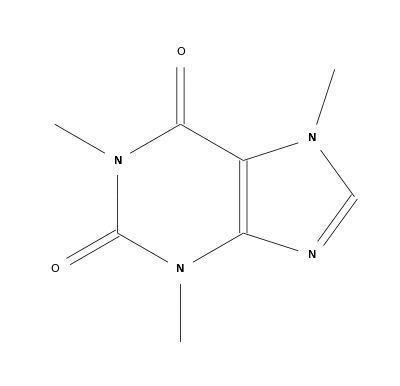

```mathematica
ChemicalData["Caffeine","StructureDiagram"]
```